## y~N(μ,σ), μ,σ~p(μ,σ|Φ) -> y~N(0,1) ∫N(y|μ,σ)p(μ,σ|Φ)dμ dσ = N(y|0,1) The above, whilst true, is useless. How to sample from p(μ,σ|Φ)? p(y,μ,σ)=N(y|μ,σ)p(μ,σ|Φ) Also, the problem as stated above does not have unique solutions, as for example, μ=δ(0) and σ=δ(1) satisfies the RHS, but so does μ~N(0,1) and σ->0. Therefore we need priors, μ, σ ~ p(μ, σ|Ψ), where Ψ is known. So the aim is to find p(μ, σ | Ψ, Ξ), where Ξ is a shorthand for the parameters of the output distribution (here N(0, 1)). Can we use Bayes’ rule? p(μ, σ | Ψ, Ξ) = p(μ, σ | Ψ, Ξ) p(μ, σ | Ψ) No. What about the joint distribution, p(μ, σ , y | Ψ, Ξ) = p(μ, σ | Ψ, Ξ) p(y | Ξ) p(μ, σ , y | Ψ, Ξ) = p(y | μ, σ) p(μ, σ| Ψ, Ξ) Ermm. We know that in the limits n -> ∞, that p(μ,σ|y1,y2,..,yn, Ψ) -> p(μ, σ|Ψ, Ξ), where yi~N(0, 1)

```mathematica
n=100000;
muSamples=RandomVariate[UniformDistribution[{-1,1}],n];
sigmaSamples=RandomVariate[UniformDistribution[{0,3}],n];
y=RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@Thread[{muSamples,sigmaSamples}];
```

```mathematica
contourVolDist=SmoothKernelDistribution[y];
```

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=RandomVariate[NormalDistribution[σ,stepSigma],{1}][[1]]},{proposedMu,proposedSigma}]
fStepAndAccept[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>1,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[PDF[RandomVariate[NormalDistribution[proposed[[1]],proposed[[2]]],{1}][[1]],
```

## Try stepping around output space and accept / rejecting as in usual Metropolis, then simulating from the posterior p(μ,σ|y_i) for each accepted y_i

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=RandomVariate[NormalDistribution[σ,stepSigma],{1}][[1]]},{proposedMu,proposedSigma}]
fStepY[y_,stepY_]:=RandomVariate[NormalDistribution[y,stepY],{1}][[1]]
fStepAcceptY[y_,stepY_]:=Block[{proposed=fStepY[y,stepY],u=RandomReal[]},If[(PDF[NormalDistribution[0,1],proposed]/PDF[NormalDistribution[0,1],y])(PDF[contourVolDist,proposed]/PDF[contourVolDist,y])>u,proposed,y]]
fStepAndAccept[y_,μ_,σ_,stepMu_,stepSigma_]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>1,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[PDF[NormalDistribution[proposed[[1]],proposed[[2]]],y]/PDF[NormalDistribution[μ,σ],y]>u,proposed,{μ,σ}]]]]
fStepYAndMuSigma[y_,μ_,σ_,stepMu_,stepSigma_,stepY_]:=Block[{y1=fStepAcceptY[y,stepY]},Join[{y1}, fStepAndAccept[y1,μ,σ,stepMu,stepSigma]]]
fWeirdSampler[numIter_Integer,y_,μ_,σ_,stepMu_,stepSigma_,stepY_]:=NestList[fStepYAndMuSigma[#[[1]],#[[2]],#[[3]],stepMu,stepSigma,stepY]&,{y,μ,σ},numIter]
```

```mathematica
samples=fWeirdSampler[10000,0,0,1,0.5,0.5,0.5];
```

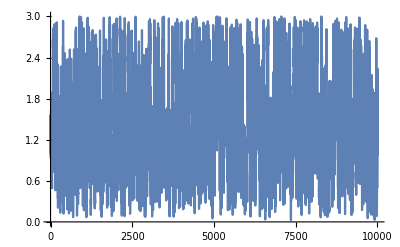

```mathematica
ListLinePlot[samples[[All,3]]]
```

```mathematica
y=RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@samples[[All,{2,3}]];
```

```mathematica
StandardDeviation@y
```

1.65649

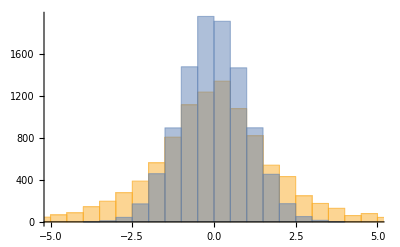

```mathematica
Histogram[{y,RandomVariate[NormalDistribution[0,1],{Length@y}]}]
```

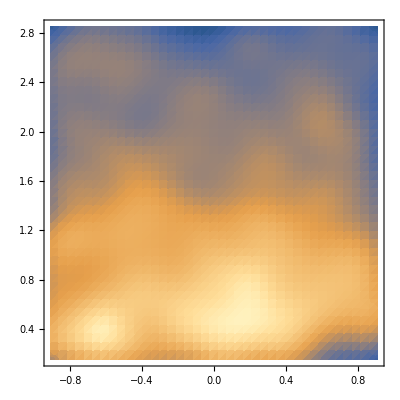

```mathematica
SmoothDensityHistogram[samples[[All,{2,3}]]]
```

## Trying Tarantola

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=σ},{proposedMu,proposedSigma}]
fEstimateIntegral[numsamples_Integer,μ_,σ_]:=Block[{d=RandomVariate[NormalDistribution[0,0.5],numsamples]},Mean[(PDF[NormalDistribution[μ,σ],#]/PDF[contourVolDist,#])&/@d]]
fStepAccept[μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>5,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[(fEstimateIntegral[numsamples,proposed[[1]],proposed[[2]]]/fEstimateIntegral[numsamples,μ,σ])>u,proposed,{μ,σ}]]]]
fTarantola[numIter_Integer,μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=NestList[fStepAccept[#[[1]],#[[2]],stepMu,stepSigma,numsamples]&,{μ,σ},numIter]
```

```mathematica
samples=ParallelTable[fTarantola[1000,0,0.5,0.4,0.4,1000],{i,1,4,1}];
```

```mathematica
samples=Flatten[samples,1];
```

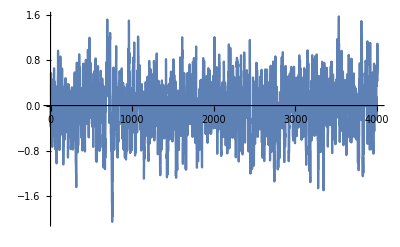

```mathematica
ListLinePlot[samples[[All,1]]]
```

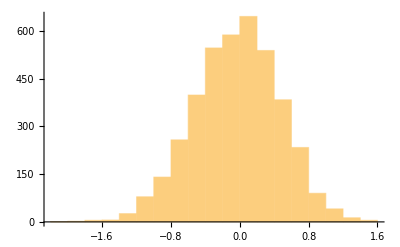

```mathematica
Histogram[samples[[All,1]]]
```

```mathematica
NIntegrate[PDF[NormalDistribution[0,1],x] PDF[NormalDistribution[0.5,1.2],x] / PDF[contourVolDist,x] ,{x,-10,10}]
```

1.10718

```mathematica
fEstimateIntegral[10000,0,3.2]
```

0.464276

## Start Tarantola again

```mathematica
n=100000;
muSamples=RandomVariate[UniformDistribution[{-1,1}],n];
y=RandomVariate[NormalDistribution[#1,0.1],{1}][[1]]&@@@muSamples;
contourVolDist=SmoothKernelDistribution[y];
```

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=σ},{proposedMu,proposedSigma}]
fEstimateIntegral[numsamples_Integer,μ_,σ_]:=Block[{d=RandomVariate[NormalDistribution[0,0.1],numsamples]},Mean[(PDF[NormalDistribution[μ,σ],#]/PDF[contourVolDist,#])&/@d]]
fStepAccept[μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>5,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[(fEstimateIntegral[numsamples,proposed[[1]],proposed[[2]]]/fEstimateIntegral[numsamples,μ,σ])>u,proposed,{μ,σ}]]]]
fTarantola[numIter_Integer,μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=NestList[fStepAccept[#[[1]],#[[2]],stepMu,stepSigma,numsamples]&,{μ,σ},numIter]
```

```mathematica
samples=ParallelTable[fTarantola[100,0,0.1,0.4,0.4,100],{i,1,4,1}];
samples=Flatten[samples,1];
```

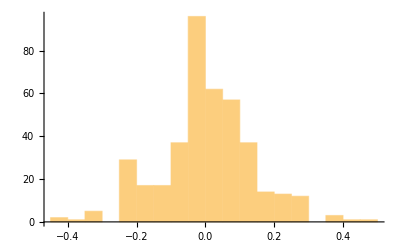

```mathematica
Histogram[samples[[All,1]]]
```

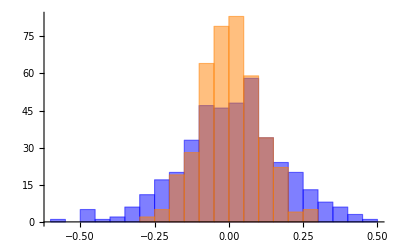

```mathematica
Histogram[{RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@samples,RandomVariate[NormalDistribution[0,0.1],{Length@samples}]},ChartStyle->{Blue,Orange}]
```

## Fredholm equation

```mathematica
eqn = PDF[NormalDistribution[0,1],d] == Integrate[PDF[NormalDistribution[mu,0.1],d] p[mu],{mu,-∞,∞}]
```

(ⅇ^(-d^2/2))/(√(2 π))==∫_(-∞)^∞ 3.98942 ⅇ^(-50. (d-mu)^2) p[mu]ⅆmu

```mathematica
sol=DSolveValue[eqn,p[x],x]
```

DSolveValue[(ⅇ^(-d^2/2))/(√(2 π))==∫_(-∞)^∞ 3.98942 ⅇ^(-50. (d-mu)^2) p[mu]ⅆmu,p[x],x]

## Answer from Stack exchange

```mathematica
Integrate[PDF[NormalDistribution[mu,1/10],d] PDF[NormalDistribution[0,Sqrt[99/100]],mu],{mu,-∞,∞}]
```

$Aborted

```mathematica
N@Sqrt[99/100]
```

0.994987

```mathematica
n=10000;
muSamples=RandomVariate[NormalDistribution[0,Sqrt[99/100]],{n}];
d=RandomVariate[NormalDistribution[#,0.1],{1}][[1]]&/@muSamples;
```

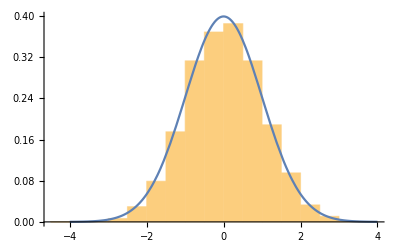

```mathematica
Show[Histogram[d,Automatic,"PDF"],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```